```mathematica
(*Problema 1:
Consideramos el soporte:*)
x0=8
x1=9
x2=10
x3=11
x4=12
x5=13
x6=14
x7=15
x8=16
```

8

9

10

11

12

13

14

15

16

```mathematica
(*y sus imágenes:*)
y0=0
y1=10
y2=15
y3=9
y4=6
y5=10
y6=8
y7=12
y8=5
```

0

10

15

9

6

10

8

12

5

```mathematica
(*Vamos a calcularlo con Lagrange:*)
l0=((x-x1)(x-x2)(x-x3)(x-x4)(x-x5)(x-x6)(x-x7)(x-x8))/((x0-x1)(x0-x2)(x0-x3)(x0-x4)(x0-x5)(x0-x6)(x0-x7)(x0-x8))
l1=((x-x0)(x-x2)(x-x3)(x-x4)(x-x5)(x-x6)(x-x7)(x-x8))/((x1-x0)(x1-x2)(x1-x3)(x1-x4)(x1-x5)(x1-x6)(x1-x7)(x1-x8))
l2=((x-x0)(x-x1)(x-x3)(x-x4)(x-x5)(x-x6)(x-x7)(x-x8))/((x2-x0)(x2-x1)(x2-x3)(x2-x4)(x2-x5)(x2-x6)(x2-x7)(x2-x8))
l3=((x-x0)(x-x1)(x-x2)(x-x4)(x-x5)(x-x6)(x-x7)(x-x8))/((x3-x0)(x3-x1)(x3-x2)(x3-x4)(x3-x5)(x3-x6)(x3-x7)(x3-x8))
l4=((x-x0)(x-x1)(x-x2)(x-x3)(x-x5)(x-x6)(x-x7)(x-x8))/((x4-x0)(x4-x1)(x4-x2)(x4-x3)(x4-x5)(x4-x6)(x4-x7)(x4-x8))
l5=((x-x0)(x-x1)(x-x2)(x-x3)(x-x4)(x-x6)(x-x7)(x-x8))/((x5-x0)(x5-x1)(x5-x2)(x5-x3)(x5-x4)(x5-x6)(x5-x7)(x5-x8))
l6=((x-x0)(x-x1)(x-x2)(x-x3)(x-x4)(x-x5)(x-x7)(x-x8))/((x6-x0)(x6-x1)(x6-x2)(x6-x3)(x6-x4)(x6-x5)(x6-x7)(x6-x8))
l7=((x-x0)(x-x1)(x-x2)(x-x3)(x-x4)(x-x5)(x-x6)(x-x8))/((x7-x0)(x7-x1)(x7-x2)(x7-x3)(x7-x4)(x7-x5)(x7-x6)(x7-x8))
l8=((x-x0)(x-x1)(x-x2)(x-x3)(x-x4)(x-x5)(x-x6)(x-x7))/((x8-x0)(x8-x1)(x8-x2)(x8-x3)(x8-x4)(x8-x5)(x8-x6)(x8-x7))
```

((-16+x) (-15+x) (-14+x) (-13+x) (-12+x) (-11+x) (-10+x) (-9+x))/40320

-((-16+x) (-15+x) (-14+x) (-13+x) (-12+x) (-11+x) (-10+x) (-8+x))/5040

((-16+x) (-15+x) (-14+x) (-13+x) (-12+x) (-11+x) (-9+x) (-8+x))/1440

-1/720 (-16+x) (-15+x) (-14+x) (-13+x) (-12+x) (-10+x) (-9+x) (-8+x)

1/576 (-16+x) (-15+x) (-14+x) (-13+x) (-11+x) (-10+x) (-9+x) (-8+x)

-1/720 (-16+x) (-15+x) (-14+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x)

((-16+x) (-15+x) (-13+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x))/1440

-((-16+x) (-14+x) (-13+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x))/5040

((-15+x) (-14+x) (-13+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x))/40320

```mathematica
(*El polinomio de Lagrange era y0*L0+y1*L1+y2*L2+...+y7*L7*)
y0*l0+y1*l1+y2*l2+y3*l3+y4*l4+y5*l5+y6*l6+y7*l7+y8*l8
```

-1/504 (-16+x) (-15+x) (-14+x) (-13+x) (-12+x) (-11+x) (-10+x) (-8+x)+1/96 (-16+x) (-15+x) (-14+x) (-13+x) (-12+x) (-11+x) (-9+x) (-8+x)-1/80 (-16+x) (-15+x) (-14+x) (-13+x) (-12+x) (-10+x) (-9+x) (-8+x)+1/96 (-16+x) (-15+x) (-14+x) (-13+x) (-11+x) (-10+x) (-9+x) (-8+x)-1/72 (-16+x) (-15+x) (-14+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x)+1/180 (-16+x) (-15+x) (-13+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x)-1/420 (-16+x) (-14+x) (-13+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x)+((-15+x) (-14+x) (-13+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x))/8064

```mathematica
Expand[%]
```

-1119329+(229222957 x)/280-(523439969 x^2)/2016+(13429973 x^3)/288-(29875237 x^4)/5760+(131701 x^5)/360-(9205 x^6)/576+(797 x^7)/2016-(19 x^8)/4480

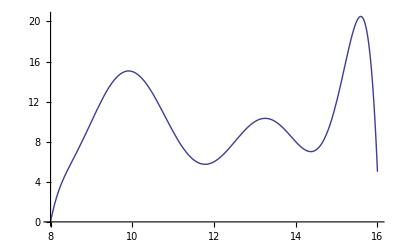

6.20016

```mathematica
(*Este era el polinomio interpolador, que hemos guardado en f[x]. La estimación en 11.5 requiere definir la función:*)
p8[x_]:=-1119329+(229222957 x)/280-(523439969 x^2)/2016+(13429973 x^3)/288-(29875237 x^4)/5760+(131701 x^5)/360-(9205 x^6)/576+(797 x^7)/2016-(19 x^8)/4480
Plot[p8[x],{x,8,16}]
p8[11.5]
```

```mathematica
(*Este es el valor de incidencias a las 11:30 horas: 6 incidencias

Comenzamos el apartado b, buscando una interpolación polinómica segmentada de grado 2. Tengamos en cuenta que para un polinomio de grado 2 necesitamos 3 puntos, Por tanto, tenemos que coger los puntos de 3 en 3. Por tanto los soportes son {x0,x1,x2}, {x2,x3,x4}, {x4,x5,x6}, {x6,x7,x8}

Empezamos con [x0,x2]*)
l0=((x-x1)(x-x2))/((x0-x1)(x0-x2))
l1=((x-x0)(x-x2))/((x1-x0)(x1-x2))
l2=((x-x0)(x-x1))/((x2-x0)(x2-x1))
Expand[y0*l0+y1*l1+y2*l2]
```

1/2 (-10+x) (-9+x)

-(-10+x) (-8+x)

1/2 (-9+x) (-8+x)

-260+(105 x)/2-(5 x^2)/2

```mathematica
f1[x_]:=-260+(105 x)/2-(5 x^2)/2
```

```mathematica
(*Ahora el intervalo [x2,x4]:*)
```

```mathematica
l2=((x-x3)(x-x4))/((x2-x3)(x2-x4))
l3=((x-x2)(x-x4))/((x3-x2)(x3-x4))
l4=((x-x2)(x-x3))/((x4-x2)(x4-x3))
Expand[y2*l2+y3*l3+y4*l4]
```

1/2 (-12+x) (-11+x)

-(-12+x) (-10+x)

1/2 (-11+x) (-10+x)

240-(75 x)/2+(3 x^2)/2

```mathematica
f2[x_]:=240-(75 x)/2+(3 x^2)/2
```

```mathematica
(*Ahora el intervalo [x4,x6]:*)
```

```mathematica
l4=((x-x5)(x-x6))/((x4-x5)(x4-x6))
l5=((x-x4)(x-x6))/((x5-x4)(x5-x6))
l6=((x-x4)(x-x5))/((x6-x4)(x6-x5))
Expand[y4*l4+y5*l5+y6*l6]
```

1/2 (-14+x) (-13+x)

-(-14+x) (-12+x)

1/2 (-13+x) (-12+x)

-510+79 x-3 x^2

```mathematica
f3[x_]:=-510+79 x-3 x^2
```

```mathematica
(*Ahora el intervalo [x6,x8]:*)
```

```mathematica
l6=((x-x7)(x-x8))/((x6-x7)(x6-x8))
l7=((x-x6)(x-x8))/((x7-x6)(x7-x8))
l8=((x-x6)(x-x7))/((x8-x6)(x8-x7))
Expand[y6*l6+y7*l7+y8*l8]
```

1/2 (-16+x) (-15+x)

-(-16+x) (-14+x)

1/2 (-15+x) (-14+x)

-1203+(327 x)/2-(11 x^2)/2

```mathematica
f4[x_]:=-1203+(327 x)/2-(11 x^2)/2
```

```mathematica
(*Creamos la función a trozos:*)
```

```mathematica
f[x_]:=Piecewise[{{f1[x],x0≤x≤x2},{f2[x],x2≤x≤x4},{f3[x],x4≤x≤x6},{f4[x],x6≤x≤x8}}]
```

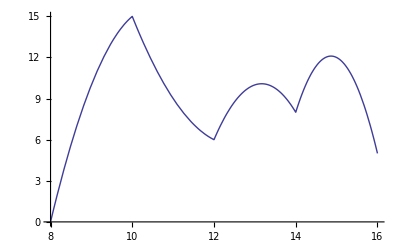

```mathematica
Plot[f[x],{x,x0,x8}]
```

```mathematica
(*En el último apartado nos piden estimar el error que se comete. POr tanto necesito dos iteraciones del polinomio interpolador. Para eso deberíamos considerar no el polinomio calculado en el primer apartado, sino uno con un elemento menos del soporte intermedio. Vamos a considerar el polinomio con {x0,...,x6,x8} y ese será el que daré finalmente en el primer apartado y el que ya habíamos calculado será el que estimaremos como exacto:*)
l0=((x-x1)(x-x2)(x-x3)(x-x4)(x-x5)(x-x6)(x-x8))/((x0-x1)(x0-x2)(x0-x3)(x0-x4)(x0-x5)(x0-x6)(x0-x8))
l1=((x-x0)(x-x2)(x-x3)(x-x4)(x-x5)(x-x6)(x-x8))/((x1-x0)(x1-x2)(x1-x3)(x1-x4)(x1-x5)(x1-x6)(x1-x8))
l2=((x-x0)(x-x1)(x-x3)(x-x4)(x-x5)(x-x6)(x-x8))/((x2-x0)(x2-x1)(x2-x3)(x2-x4)(x2-x5)(x2-x6)(x2-x8))
l3=((x-x0)(x-x1)(x-x2)(x-x4)(x-x5)(x-x6)(x-x8))/((x3-x0)(x3-x1)(x3-x2)(x3-x4)(x3-x5)(x3-x6)(x3-x8))
l4=((x-x0)(x-x1)(x-x2)(x-x3)(x-x5)(x-x6)(x-x8))/((x4-x0)(x4-x1)(x4-x2)(x4-x3)(x4-x5)(x4-x6)(x4-x8))
l5=((x-x0)(x-x1)(x-x2)(x-x3)(x-x4)(x-x6)(x-x8))/((x5-x0)(x5-x1)(x5-x2)(x5-x3)(x5-x4)(x5-x6)(x5-x8))
l6=((x-x0)(x-x1)(x-x2)(x-x3)(x-x4)(x-x5)(x-x8))/((x6-x0)(x6-x1)(x6-x2)(x6-x3)(x6-x4)(x6-x5)(x6-x8))
l8=((x-x0)(x-x1)(x-x2)(x-x3)(x-x4)(x-x5)(x-x6))/((x8-x0)(x8-x1)(x8-x2)(x8-x3)(x8-x4)(x8-x5)(x8-x6))
```

-((-16+x) (-14+x) (-13+x) (-12+x) (-11+x) (-10+x) (-9+x))/5760

1/840 (-16+x) (-14+x) (-13+x) (-12+x) (-11+x) (-10+x) (-8+x)

-1/288 (-16+x) (-14+x) (-13+x) (-12+x) (-11+x) (-9+x) (-8+x)

1/180 (-16+x) (-14+x) (-13+x) (-12+x) (-10+x) (-9+x) (-8+x)

-1/192 (-16+x) (-14+x) (-13+x) (-11+x) (-10+x) (-9+x) (-8+x)

1/360 (-16+x) (-14+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x)

-((-16+x) (-13+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x))/1440

((-14+x) (-13+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x))/40320

```mathematica
y0*l0+y1*l1+y2*l2+y3*l3+y4*l4+y5*l5+y6*l6+y8*l8
```

1/84 (-16+x) (-14+x) (-13+x) (-12+x) (-11+x) (-10+x) (-8+x)-5/96 (-16+x) (-14+x) (-13+x) (-12+x) (-11+x) (-9+x) (-8+x)+1/20 (-16+x) (-14+x) (-13+x) (-12+x) (-10+x) (-9+x) (-8+x)-1/32 (-16+x) (-14+x) (-13+x) (-11+x) (-10+x) (-9+x) (-8+x)+1/36 (-16+x) (-14+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x)-1/180 (-16+x) (-13+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x)+((-14+x) (-13+x) (-12+x) (-11+x) (-10+x) (-9+x) (-8+x))/8064

```mathematica
Expand[%]
```

54415-(1559983 x)/56+(8124497 x^2)/1440-(199631 x^3)/360+(27463 x^4)/1152+(65 x^5)/1152-(223 x^6)/5760+(37 x^7)/40320

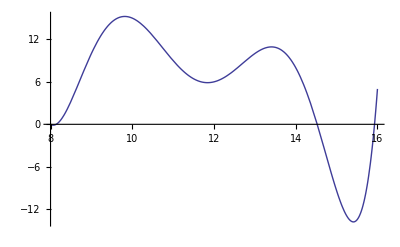

6.435

```mathematica
p7[x_]:=54415-(1559983 x)/56+(8124497 x^2)/1440-(199631 x^3)/360+(27463 x^4)/1152+(65 x^5)/1152-(223 x^6)/5760+(37 x^7)/40320
Plot[p7[x],{x,x0,x8}]
p7[11.5]
```

```mathematica
Abs[p8[x]-p7[x]]
```

Abs[-1173744+(29627859 x)/35-(74279759 x^2)/280+(7549821 x^3)/160-(416841 x^4)/80+(234099 x^5)/640-(10203 x^6)/640+(1767 x^7)/4480-(19 x^8)/4480]

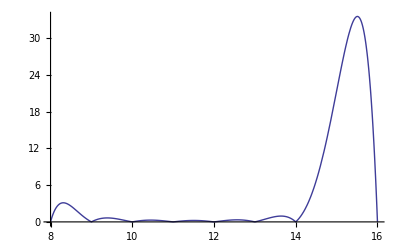

```mathematica
Plot[%,{x,x0,x8},PlotRange->Full]
```

```mathematica
(*Para el punto en cuestión 11.5, el error sería:)
```

```mathematica
Abs[p8[11.5]-p7[11.5]]
```

0.234833

```mathematica
(*Problema 2
Usamos Lagrange como antes*)
t0=0
t1=8
t2=2
t3=4
t4=6
```

0

8

2

4

6

```mathematica
vA0=0
vA1=38
vA2=17
vA3=27
vA4=34
```

0

38

17

27

34

```mathematica
l0=((t-t1)(t-t2)(t-t3)(t-t4))/((t0-t1)(t0-t2)(t0-t3)(t0-t4))
l1=((t-t0)(t-t2)(t-t3)(t-t4))/((t1-t0)(t1-t2)(t1-t3)(t1-t4))
l2=((t-t0)(t-t1)(t-t3)(t-t4))/((t2-t0)(t2-t1)(t2-t3)(t2-t4))
l3=((t-t0)(t-t1)(t-t2)(t-t4))/((t3-t0)(t3-t1)(t3-t2)(t3-t4))
l4=((t-t0)(t-t1)(t-t2)(t-t3))/((t4-t0)(t4-t1)(t4-t2)(t4-t3))
```

1/384 (-8+t) (-6+t) (-4+t) (-2+t)

1/384 (-6+t) (-4+t) (-2+t) t

-1/96 (-8+t) (-6+t) (-4+t) t

1/64 (-8+t) (-6+t) (-2+t) t

-1/96 (-8+t) (-4+t) (-2+t) t

```mathematica
vA0*l0+vA1*l1+vA2*l2+vA3*l3+vA4*l4
```

-17/96 (-8+t) (-6+t) (-4+t) t+27/64 (-8+t) (-6+t) (-2+t) t-17/48 (-8+t) (-4+t) (-2+t) t+19/192 (-6+t) (-4+t) (-2+t) t

```mathematica
Expand[%]
```

(137 t)/12-(11 t^2)/6+(5 t^3)/24-t^4/96

```mathematica
(*Este es el polinomio de Lagrange

Vamos al apartado b para usar Newton para 4 punto
ORDEN 0*)
vB0=0
vB1=26
vB2=11
vB3=17
vB4=22
```

0

26

11

17

22

```mathematica
(*ORDEN 1*)
vB01=(vB1-vB0)/(t1-t0)
vB12=(vB2-vB1)/(t2-t1)
vB23=(vB3-vB2)/(t3-t2)
vB34=(vB4-vB3)/(t4-t3)
```

13/4

5/2

3

5/2

```mathematica
(*ORDEN 2*)
```

```mathematica
vB012=(vB12-vB01)/(t2-t0)
vB123=(vB23-vB12)/(t3-t1)
vB234=(vB34-vB23)/(t4-t2)
```

-3/8

-1/8

-1/8

```mathematica
(*ORDEN 3*)
```

```mathematica
vB0123=(vB123-vB012)/(t3-t0)
vB1234=(vB234-vB123)/(t4-t1)
```

1/16

0

```mathematica
vB01234=(vB1234-vB0123)/(t4-t0)
```

-1/96

```mathematica
(*Polinomio con 4 puntos:*)
vB0+vB01(t-t0)+vB012(t-t0)(t-t1)+vB0123(t-t0)(t-t1)(t-t2)
```

(13 t)/4-3/8 (-8+t) t+1/16 (-8+t) (-2+t) t

```mathematica
Expand[%]
```

(29 t)/4-t^2+t^3/16

```mathematica
(*Con 5 puntos:*)
%+vB01234(t-t0)(t-t1)(t-t2)(t-t3)
```

(29 t)/4-1/96 (-8+t) (-4+t) (-2+t) t-t^2+t^3/16

```mathematica
Expand[%]
```

(95 t)/12-(19 t^2)/12+(5 t^3)/24-t^4/96

```mathematica
(*Para interpolación de Hermite consideramos el soporte ordenado*)
t0=0
t1=2
t2=4
t3=6
t4=8
```

0

2

4

6

8

```mathematica
vA0=0
vA1=17
vA2=27
vA3=34
vA4=38
```

0

17

27

34

38

```mathematica
(*Para la aceleración media consideramos que*)
aA0=0 (*porque es cuando empieza*)
aA1=(vA1-vA0)/(t1-t0)
aA2=(vA2-vA1)/(t2-t1)
aA3=(vA3-vA2)/(t3-t2)
aA4=(vA4-vA3)/(t4-t3)
```

0

17/2

5

7/2

2

```mathematica
(*Duplicamos el soporte {z0,z1,z2,z3,z4,z5,z6,z7,z8,z9} y tomamos las diferencias de ORDEN 0:*)
dif0=vA0
dif1=vA0
dif2=vA1
dif3=vA1
dif4=vA2
dif5=vA2
dif6=vA3
dif7=vA3
dif8=vA4
dif9=vA4
```

0

0

17

17

27

27

34

34

38

38

```mathematica
(*ORDEN 1*)
dif01=aA0
dif12=(dif2-dif1)/(t1-t0)
dif23=aA1
dif34=(dif4-dif3)/(t2-t1)
dif45=aA2
dif56=(dif6-dif5)/(t3-t2)
dif67=aA3
dif78=(dif8-dif7)/(t4-t3)
dif89=aA4
```

0

17/2

17/2

5

5

7/2

7/2

2

2

```mathematica
(*ORDEN 2*)
dif012=(dif12-dif01)/(t1-t0)
dif123=(dif23-dif12)/(t1-t0)
dif234=(dif34-dif23)/(t2-t1)
dif345=(dif45-dif34)/(t2-t1)
dif456=(dif56-dif45)/(t3-t2)
dif567=(dif67-dif56)/(t3-t2)
dif678=(dif78-dif67)/(t4-t3)
dif789=(dif89-dif78)/(t4-t3)
```

17/4

0

-7/4

0

-3/4

0

-3/4

0

```mathematica
(*ORDEN 3*)
dif0123=(dif123-dif012)/(t1-t0)
dif1234=(dif234-dif123)/(t2-t0)
dif2345=(dif345-dif234)/(t2-t1)
dif3456=(dif456-dif345)/(t3-t1)
dif4567=(dif567-dif456)/(t3-t2)
dif5678=(dif678-dif567)/(t4-t2)
dif6789=(dif789-dif678)/(t4-t3)
```

-17/8

-7/16

7/8

-3/16

3/8

-3/16

3/8

```mathematica
(*ORDEN 4*)
dif01234=(dif1234-dif0123)/(t2-t0)
dif12345=(dif2345-dif1234)/(t2-t0)
dif23456=(dif3456-dif2345)/(t3-t1)
dif34567=(dif4567-dif3456)/(t3-t1)
dif45678=(dif5678-dif4567)/(t4-t2)
dif56789=(dif6789-dif5678)/(t4-t2)
```

27/64

21/64

-17/64

9/64

-9/64

9/64

```mathematica
(*ORDEN 5*)
dif012345=(dif12345-dif01234)/(t2-t0)
dif123456=(dif23456-dif12345)/(t3-t0)
dif234567=(dif34567-dif23456)/(t3-t1)
dif345678=(dif45678-dif34567)/(t4-t1)
dif456789=(dif56789-dif45678)/(t4-t2)
```

-3/128

-19/192

13/128

-3/64

9/128

```mathematica
(*ORDEN 6*)
dif0123456=(dif123456-dif012345)/(t3-t0)
dif1234567=(dif234567-dif123456)/(t3-t0)
dif2345678=(dif345678-dif234567)/(t4-t1)
dif3456789=(dif456789-dif345678)/(t4-t1)
```

-29/2304

77/2304

-19/768

5/256

```mathematica
(*ORDEN 7*)
dif01234567=(dif1234567-dif0123456)/(t3-t0)
dif12345678=(dif2345678-dif1234567)/(t4-t0)
dif23456789=(dif3456789-dif2345678)/(t4-t1)
```

53/6912

-67/9216

17/2304

```mathematica
(*ORDEN 8*)
dif012345678=(dif12345678-dif01234567)/(t4-t0)
dif123456789=(dif23456789-dif12345678)/(t4-t0)
```

-413/221184

15/8192

```mathematica
(*ORDEN 8*)
dif0123456789=(dif123456789-dif012345678)/(t4-t0)
```

409/884736

```mathematica
dif0+dif01(t-t0)+dif012(t-t0)(t-t0)+dif0123(t-t0)(t-t0)(t-t1)+dif01234(t-t0)(t-t0)(t-t1)(t-t1)+dif012345(t-t0)(t-t0)(t-t1)(t-t1)(t-t2)+dif0123456(t-t0)(t-t0)(t-t1)(t-t1)(t-t2)(t-t2)+dif01234567(t-t0)(t-t0)(t-t1)(t-t1)(t-t2)(t-t2)(t-t3)+dif012345678(t-t0)(t-t0)(t-t1)(t-t1)(t-t2)(t-t2)(t-t3)(t-t3)+dif0123456789(t-t0)(t-t0)(t-t1)(t-t1)(t-t2)(t-t2)(t-t3)(t-t3)(t-t4)
```

(17 t^2)/4-17/8 (-2+t) t^2+27/64 (-2+t)^2 t^2-3/128 (-4+t) (-2+t)^2 t^2-(29 (-4+t)^2 (-2+t)^2 t^2)/2304+(53 (-6+t) (-4+t)^2 (-2+t)^2 t^2)/6912-(413 (-6+t)^2 (-4+t)^2 (-2+t)^2 t^2)/221184+(409 (-8+t) (-6+t)^2 (-4+t)^2 (-2+t)^2 t^2)/884736

```mathematica
Expand[%]
```

-(577 t^2)/96+(91267 t^3)/3456-(308449 t^4)/13824+(493097 t^5)/55296-(54587 t^6)/27648+(27481 t^7)/110592-(3685 t^8)/221184+(409 t^9)/884736

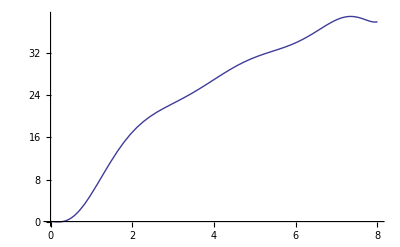

```mathematica
Plot[%,{t,t0,t4}]
```

```mathematica
(*Problema 3: El intervalo [-2,2] tiene amplitud 4
Para 4 puntos, estamos hablando que el intervalo se divide entre 3*)
x0=-2
x1=-2+4/3
x2=-2+2*4/3
x3=-2+3*4/3
f[x_]:=2/(3+5x^2)
```

-2

-2/3

2/3

2

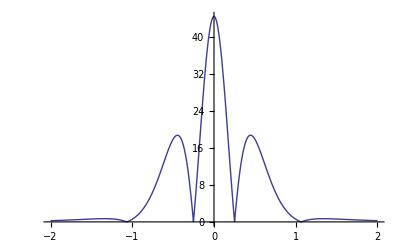

```mathematica
(*La fórmula es (|f^(4))|)/(4!)|x-x0||x-x1||x-x2||x-x3|. Por tanto primero corres ponde a estudiar la derivada en dicho intervalo:*)
Plot[Abs[f''''[x]],{x,-2,2}]
```

```mathematica
f'''''[x]
```

-(24000000 x^5)/((3+5 x^2)^6)+(4800000 x^3)/((3+5 x^2)^5)-(180000 x)/((3+5 x^2)^4)

```mathematica
Solve[%==0]
```

{{x→0},{x→-3/(√5)},{x→-1/(√5)},{x→1/(√5)},{x→3/(√5)}}

```mathematica
(*La derivada cuarta tiene el máximo en un punto intermedio del intervalo. Calculamos la derivada 5 y comprobamos que el punto crítico buscado es x=0 tal y como vemos en la gráfica:*)
errorPolGrad3[x_]=Abs[f''''[0]]/4!Abs[(x-x0)(x-x1)(x-x2)(x-x3)]
```

50/27 Abs[(-2+x) (-2/3+x) (2/3+x) (2+x)]

```mathematica
(*Esta es la expresión del error para 4 puntos

Para 5 puntos el soporte se obtiene con 4 intervalos y por tanto el soporte es*)
x0=-2
x1=-1
x2=0
x3=1
x4=2
```

-2

-1

0

1

2

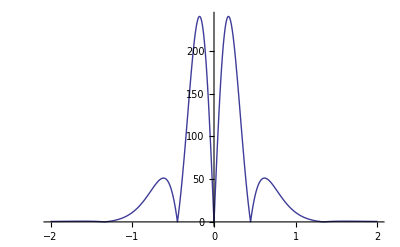

```mathematica
(*La fórmula del error absoluto es (|f^(5))|)/(5!)|x-x0||x-x1||x-x2||x-x3||x-x4|. Por tanto primero corres ponde a estudiar la derivada en dicho intervalo:*)
Plot[Abs[f'''''[x]],{x,-2,2},PlotRange->Full]
```

```mathematica
(*La derivada quinta tiene dos máximo en la zona media. Vamos a ver los puntos críticos:*)
f''''''[x]
```

(1440000000 x^6)/((3+5 x^2)^7)-(360000000 x^4)/((3+5 x^2)^6)+(21600000 x^2)/((3+5 x^2)^5)-180000/((3+5 x^2)^4)

```mathematica
NSolve[%==0]
```

{{x→-1.60847},{x→1.60847},{x→-0.61772},{x→0.61772},{x→-0.176797},{x→0.176797}}

```mathematica
(*El máximo es el más cercano al x=0, por lo que el error lo estimaremos como:*)
Abs[f'''''[0.17679663503871393]]/5!Abs[(x-x0)(x-x1)(x-x2)(x-x3)(x-x4)]
```

2.00142 Abs[(-2+x) (-1+x) x (1+x) (2+x)]

```mathematica
(*Esta es la expresión del error para 5 puntos que corresponde a P4. Por tanto, el apartado siguiente me pide sustituir x=1.2 en la expresión del error P3:*)
errorPolGrad3[1.2]
```

4.71967

-2

-2/3

2/3

2

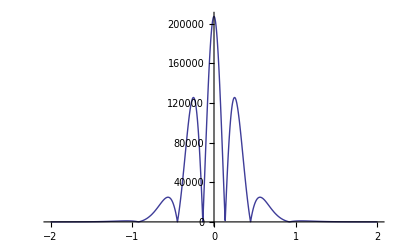

```mathematica
(*Veamos ahora el error absoluto cometido con Hermite para cuatro puntos: (|f^(8))|)/(8!)|x-x0|^2|x-x1|^2|x-x2|^2|x-x3|^2*)
x0=-2
x1=-2+4/3
x2=-2+2*4/3
x3=-2+3*4/3
Plot[Abs[f''''''''[x]],{x,-2,2},PlotRange->Full]
```

```mathematica
(*La derivada octava parece tener un máximo en la zona media. Vamos a ver los puntos críticos:*)
```

```mathematica
Solve[f'''''''''[x]==0]
```

{{x→0},{x→-√(3/5+6/(5 √5))},{x→√(3/5+6/(5 √5))},{x→-√(3/5 (5-2 √5))},{x→√(3/5 (5-2 √5))},{x→-1/5 √(3 (5-2 √5))},{x→1/5 √(3 (5-2 √5))},{x→-√(3/5 (5+2 √5))},{x→√(3/5 (5+2 √5))}}

```mathematica
(*Es en el x=0. Luego la expresión del error será:*)
Abs[f''''''''[0]]/8!(x-x0)^2(x-x1)^2(x-x2)^2(x-x3)^2
```

1250/243 (-2+x)^2 (-2/3+x)^2 (2/3+x)^2 (2+x)^2

-2

-1

0

1

2

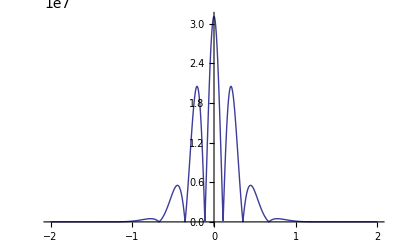

```mathematica
(*Para 5 puntosahora el error absoluto cometido con Hermite para cuatro puntos: (|f^(10))|)/(10!)|x-x0|^2|x-x1|^2|x-x2|^2|x-x3|^2|x-x4|^2*)
x0=-2
x1=-1
x2=0
x3=1
x4=2
Plot[Abs[f''''''''''[x]],{x,-2,2},PlotRange->Full]
```

```mathematica
(*Veamos que el máximo es otra vez x=0. En efecto:*)
Solve[f'''''''''''[x]==0]
```

{{x→0},{x→-√(3/5)},{x→√(3/5)},{x→-3/(√5)},{x→-1/(√5)},{x→1/(√5)},{x→3/(√5)},{x→-√(3/5 (7-4 √3))},{x→√(3/5 (7-4 √3))},{x→-√(21/5+(12 √3)/5)},{x→√(21/5+(12 √3)/5)}}

```mathematica
(*El error absoluto se expresa como:*)
Abs[f''''''''''[0]]/10!(x-x0)^2(x-x1)^2(x-x2)^2(x-x3)^2(x-x4)^2
```

6250/729 (-2+x)^2 (-1+x)^2 x^2 (1+x)^2 (2+x)^2

```mathematica
(*Pasamos al cálculo del polinomio interpolador por 3 puntos equiespaciados y por Newton*)
x0=-2
x1=0
x2=2
```

-2

0

2

```mathematica
(*Diferencias orden 0:*)
dif0=f[x0]
dif1=f[x1]
dif2=f[x2]
```

2/23

2/3

2/23

```mathematica
(*Diferencias de orden 1:*)
dif01=(dif1-dif0)/(x1-x0)
dif12=(dif2-dif1)/(x2-x1)
```

20/69

-20/69

```mathematica
(*Diferencia de orden 2:*)
dif012=(dif12-dif01)/(x2-x0)
```

-10/69

```mathematica
(*El polinomio es:*)
dif0+dif01(x-x0)+dif012(x-x0)(x-x1)
```

2/23+(20 (2+x))/69-10/69 x (2+x)

```mathematica
Expand[%]
```

2/3-(10 x^2)/69

```mathematica
(*Vamos a la interpolacion de Hermite:*)
z0=x0
z1=x0
z2=x1
z3=x1
z4=x2
z5=x2
```

-2

-2

0

0

2

2

```mathematica
(*ORDEN 0*)
dif0=f[z0]
dif1=f[z1]
dif2=f[z2]
dif3=f[z3]
dif4=f[z4]
dif5=f[z5]
```

2/23

2/23

2/3

2/3

2/23

2/23

```mathematica
(*ORDEN 1*)
dif01=f'[z0]
dif12=(dif2-dif1)/(z2-z1)
dif23=f'[z2]
dif34=(dif4-dif3)/(z4-z3)
dif45=f'[z4]
```

40/529

20/69

0

-20/69

-40/529

```mathematica
(*ORDEN 2*)
dif012=(dif12-dif01)/(z2-z0)
dif123=(dif23-dif12)/(z3-z1)
dif234=(dif34-dif23)/(z4-z2)
dif345=(dif45-dif34)/(z5-z3)
```

170/1587

-10/69

-10/69

170/1587

```mathematica
(*ORDEN 3*)
dif0123=(dif123-dif012)/(z3-z0)
dif1234=(dif234-dif123)/(z4-z1)
dif2345=(dif345-dif234)/(z5-z2)
```

-200/1587

0

200/1587

```mathematica
(*ORDEN 4*)
dif01234=(dif1234-dif0123)/(z4-z0)
dif12345=(dif2345-dif1234)/(z5-z1)
```

50/1587

50/1587

```mathematica
(*ORDEN 5*)
dif012345=(dif12345-dif01234)/(z5-z0)
```

0

```mathematica
(*El polinomio de Hermite es:*)
dif0+dif01(x-z0)+dif012(x-z0)(x-z1)+dif0123(x-z0)(x-z1)(x-z2)+dif01234(x-z0)(x-z1)(x-z2)(x-z3)+dif012345(x-z0)(x-z1)(x-z2)(x-z3)(x-z4)
```

2/23+(40 (2+x))/529+(170 (2+x)^2)/1587-(200 x (2+x)^2)/1587+(50 x^2 (2+x)^2)/1587

```mathematica
Expand[%]
```

2/3-(430 x^2)/1587+(50 x^4)/1587